```mathematica
<<OrbitalMotion`
```

## Test nearest point calculation

```mathematica
rL = {1,2,3};
d = {1,1,-0.5};
```

```mathematica
nearest[t_]:=rL + t d
```

```mathematica
tt = -Dot[rL,d]/Dot[d,d]
```

-0.666667

```mathematica
nearest[tt]
```

{0.333333,1.33333,3.33333}

```mathematica
Manipulate[
Show[
ParametricPlot3D[rL + t d,{t,-10,10}],
Graphics3D[{Red, PointSize[0.02], Point[nearest[tt]]}],
Graphics3D[{PointSize[0.02], Point[nearest[tUser]]}],
Graphics3D[{Line[{{0,0,0},nearest[tUser]}]}]
]
,{tUser,-10,10}]
```

## Spacecraft Access Test

```mathematica
r= reqEarth + 1000.;
angle = 90. Degree;
zScale = {1,2};
```

```mathematica
rB = r {1,0}
rS = r{Cos[angle], Sin[angle]}
rSB = rS - rB
```

{7378.14,0.}

{4.51781×10^-13,7378.14}

{-7378.14,7378.14}

```mathematica
param = -Dot[rSB zScale, rB zScale]/Dot[rSB zScale, rSB zScale]
```

0.2

```mathematica
rClose = (rB  + param rSB )  zScale
```

{5902.51,2951.25}

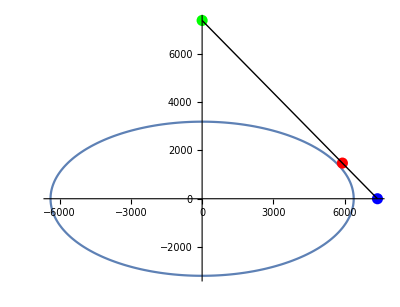

```mathematica
Show[
ParametricPlot[reqEarth{Cos[t],  Sin[t]}/zScale, {t,0,2 π}]
, Graphics[{PointSize[0.02],Blue, Point[rB]}]
,Graphics[{PointSize[0.02],Green, Point[rS]}]
, Graphics[{PointSize[0.02], Red, Point[rClose /zScale]}]
,Graphics[{Line[{rB, rS}]}]
,PlotRange->All
]
```

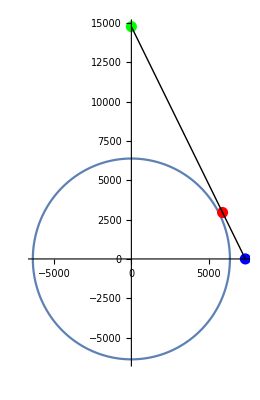

```mathematica
Show[
ParametricPlot[reqEarth{Cos[t],  Sin[t]}, {t,0,2 π}]
, Graphics[{PointSize[0.02],Blue, Point[rB zScale]}]
,Graphics[{PointSize[0.02],Green, Point[rS zScale]}]
, Graphics[{PointSize[0.02], Red, Point[rClose]}]
,Graphics[{Line[{rB zScale, rS zScale}]}]
,PlotRange->All
]
```